```mathematica
ariasD[0] = 1;
ariasD[n_Integer?Positive] := ariasD[n] = Sum[2^((k (k - 1) - n (n - 1))/2) ariasD[k]/(n - k + 1)!, {k, 0, n - 1}]/(2^n - 1);
iFabiusF[x_]:=Module[{prec=Precision[x],n,p,q,s,tol,w,y,z},If[x<0,Return[0,Module]];tol=10^(-prec);
z=SetPrecision[x,Infinity];s=1;y=0;
z=If[0≤z≤2,1-Abs[1-z],q=Quotient[z,2];
If[ThueMorse[q]==1,s=-1];
1-Abs[1-z+2 q]];
While[z>0,n=-Floor[RealExponent[z,2]];p=2^n;
z-=1/p;w=1;
Do[w=ariasD[m]+p z w/(n-m+1);p/=2,{m,n}];
y=w-y;
If[Abs[w]<Abs[y] tol,Break[]]];
SetPrecision[s Abs[y],prec]];
FabiusF[Infinity] = Interval[{-1, 1}];
FabiusF[x_?NumberQ] /; If[Im[x] == 0, TrueQ[Composition[BitAnd[#, # - 1] &, Denominator][x] == 0], False] := iFabiusF[x];
Derivative[n_Integer][FabiusF] := 2^(n (n + 1)/2) FabiusF[2^n #] &;
SetAttributes[FabiusF, {NumericFunction, Listable}];//Timing//AbsoluteTiming;
```

```mathematica
ClearAll[iCurvaturePlotHelper,CurvaturePlot]
iCurvaturePlotHelper[f_?(Head[#]=!=List&),{t_,tmin_,tmax_},{{x0_,y0_},θ0_},opts:OptionsPattern[]]:=Module[{sol,θ,x,y,if},sol=NDSolve[{θ'[t]==f,x'[t]==Cos[θ[t]],y'[t]==Sin[θ[t]],θ[tmin]==θ0,x[tmin]==x0,y[tmin]==y0},{x,y},{t,tmin,tmax},opts];
if={x[#],y[#]}&/.First[sol];
if]
CurvaturePlot[f_,{t_,tmin_,tmax_},opts:OptionsPattern[]]:=CurvaturePlot[f,{t,tmin,tmax},{{0,0},0},opts]
CurvaturePlot[f_,{t_,tmin_,tmax_},p:{{x0_,y0_},θ0_},opts:OptionsPattern[]]:=Module[{θ,x,y,sol,rlsplot,rlsndsolve,if,ifs},rlsplot=FilterRules[{opts},Options[ParametricPlot]];
rlsndsolve=FilterRules[{opts},Options[NDSolve]];
If[Head[f]===List,ifs=iCurvaturePlotHelper[#,{t,tmin,tmax},p,Evaluate@(Sequence@@rlsndsolve)]&/@f;
ParametricPlot[Evaluate[#[tplot]&/@ifs],{tplot,tmin,tmax},Evaluate@(Sequence@@rlsplot)],if=iCurvaturePlotHelper[f,{t,tmin,tmax},p,Evaluate@(Sequence@@rlsndsolve)];
ParametricPlot[Evaluate[if[tplot]],{tplot,tmin,tmax},Evaluate@(Sequence@@rlsplot)]]]
```

```mathematica
(*ᔓᔕ={MaxRecursion->0,PlotPoints->1+2^8,Ticks->{Automatic,Automatic},ImageSize->Full,PlotRange->Full};
Show[
CurvaturePlot[Cos[X],{X,0,4 π},Evaluate[ᔓᔕ]]
,
Plot[(-Cos[X*Pi/2.4039598877241946]/2+.5)*1.7867179537183144,{X,0,4*π/Pi*2.4039598877241946},Evaluate[ᔓᔕ]]
,
Evaluate[ᔓᔕ]
]*)
```

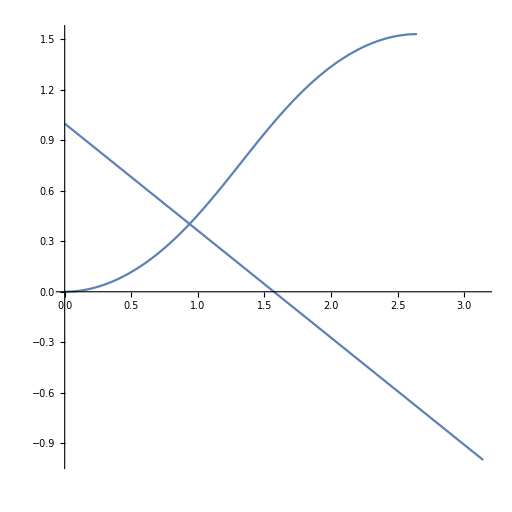

{{{0.000003141592653589793,0.999998},{3.14158951199714,-0.999998}}}
{{{0.,0.},{2.644715082726751,1.531824801015901}}}

```mathematica
ᑫᑭ={MaxRecursion->0,PlotPoints->1+2^0};
ᔓᔕ={MaxRecursion->0,PlotPoints->1+2^8,Ticks->{Automatic,Automatic},ImageSize->512,PlotRange->Full,AspectRatio->1};
ᖆᖇ=4*ArcTan[1]*1;
ᗩ={X,0,Pi};
(*ꗳ=-TriangleWave[X/ᖆᖇ*.5-.25]/1;*)
ꗳ=-(X-(Pi/2))/(Pi/2);
Show[
CurvaturePlot[Evaluate[ꗳ],Evaluate[ᗩ],Evaluate[ᔓᔕ]]
,
Plot[Evaluate[ꗳ],Evaluate[ᗩ],Evaluate[ᔓᔕ]]
,
Evaluate[ᔓᔕ]
]
DecimalForm[N[TableForm[{Flatten[DecimalForm[N[Cases[Plot[Evaluate[ꗳ],Evaluate[ᗩ],Evaluate[ᑫᑭ]],Line[X__]->X,Infinity],1],256]]
,
Flatten[DecimalForm[N[Cases[CurvaturePlot[Evaluate[ꗳ],Evaluate[ᗩ],Evaluate[ᑫᑭ]],Line[X__]->X,Infinity],1],256]]
}]],256]
```

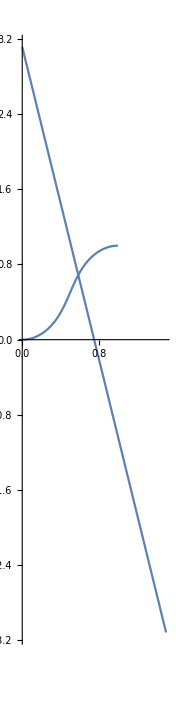

{{{0.00000150389099015843,3.114757622170496},{1.50388948626744,-3.114757622170496}}}
{{{0.,0.},{1.00000000000001,1.000000000000003}}}

```mathematica
ᑫᑭ={MaxRecursion->0,PlotPoints->1+2^0};
ᔓᔕ={MaxRecursion->0,PlotPoints->1+2^8,Ticks->{Automatic,Automatic},ImageSize->176,PlotRange->Full,AspectRatio->4};
ᖆᖇ={X,0,Pi/(2.088976311546913772239187217936)};
ꗳ=(((Pi/2)-X*(2.088976311546913772239187217936))/(Pi/2)*1.4910479522822721)*(2.088976311546913772239187217936);
Show[    CurvaturePlot[Evaluate[ꗳ],Evaluate[ᖆᖇ],Evaluate[ᔓᔕ]]    ,    Plot[Evaluate[ꗳ],Evaluate[ᖆᖇ],Evaluate[ᔓᔕ]]    ,    Evaluate[ᔓᔕ]    ]
TableForm[{
Flatten[DecimalForm[N[Cases[Plot[Evaluate[ꗳ],Evaluate[ᖆᖇ],Evaluate[ᑫᑭ]],Line[X__]->X,Infinity],1],256]]
,
Flatten[DecimalForm[N[Cases[CurvaturePlot[Evaluate[ꗳ],Evaluate[ᖆᖇ],Evaluate[ᑫᑭ]],Line[X__]->X,Infinity],1],256]]
}]
```